```mathematica
p1[x_]:= a1*x^3+b1*x^2+c1*x+d1
p2[x_] := a2*x^3+b2*x^2+c2*x+d2
p3[x_] := 0.5
p4[x_] := a4*x^3+b4*x^2+c4*x+d4
p5[x_] :=0.075*x-0.55
p6[x_] := a6*x^3+b6*x^2+c6*x+d6
p7[x_]:=1.25
p8[x_] := a8*x^3+b8*x^2+c8*x+d8
p9[x_]:= -0.5*x+17.75
```

```mathematica
Solve[{p1[0]==.75,p1[1/2]==1.25, p1[1]==0.5,p1'[1/2]==0},{a1,b1,c1,d1}]
```

{{a1→-1.,b1→-1.,c1→1.75,d1→0.75}}

```mathematica
Solve[{p2[0.5] ==p1[0.5],p2[1.5]==p3[1.5],p2'[0.5]==p1'[0.5],p2'[1.5]==p3'[1.5]},{a2,b2,c2,d2}]
```

{{a2→-1.+1. a1+1.5 b1+2. c1+2. d1,b2→3.-3.375 a1-5. b1-6.5 c1-6. d1,c2→-2.25+3.375 a1+4.875 b1+6. c1+4.5 d1,d2→0.5-0.84375 a1-1.125 b1-1.125 c1}}

```mathematica
Solve[{p4[10] ==p3[10],p4[18]==p5[18],p4'[10]==p3'[10],p4'[18]==p5'[18]},{a4,b4,c4,d4}]
```

{{a4→6.50521×10^-19,b4→0.0046875,c4→-0.09375,d4→0.96875}}

```mathematica
Solve[{p6[21] ==p5[21],p6[26]==p7[26],p6'[21]==p5'[21],p6'[26]==p7'[26]},{a6,b6,c6,d6}]
```

{{a6→-0.0006,b6→0.0348,c6→-0.5928,d6→3.6836}}

```mathematica
Solve[{p8[32] ==p7[32],p8[33.5]==p9[33.5],p8'[32]==p7'[32], p8'[33.5] == p9'[33.5]},{a8,b8,c8,d8}]
```

{{a8→-0.0740741,b8→7.11111,c8→-227.556,d8→2428.51}}

```mathematica
p1[x_] := -1*x^3-1*x^2 + 1.75*x + 0.75
p2[x_] :=1.5*x^3+-4.5*x^2 + 3.375*x + 0.5
p4[x_]:=0.004687499999999973*x^2-0.09374999999999964*x+0.9687499999999986
p6[x_]:= -0.0006*x^3+0.034800000000000005*x^2-0.5928000000000003*x +3.6836000000000015
p8[x_]:= -0.07407407407408549*x^3+7.111111111112233*x^2-227.5555555555923*x+2428.509259259659
```

```mathematica
spline[x_]:= Piecewise[{{p1[x], 0≤ x< 0.5},{p2[x], 0.5≤ x<1.5},{p3[x],1.5≤ x< 10},{p4[x],10≤x<18},{p5[x],18≤x<21},{p6[x],21≤x<26},{p7[x],26≤ x<32},{p8[x], 32≤x≤33.5}}]
```

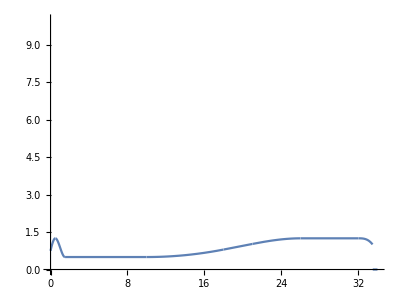

```mathematica
Plot[spline[x],{x,0,34}, AspectRatio->.75, PlotRange->{0,10}]
```

```mathematica
RevolutionPlot3D[spline[x],{x,0,33.5},RevolutionAxis->{1,0,0}]
```

-Graphics3D-